```mathematica
Clear[α,ϵ,  matrix, r]
$Assumptions={Element[{ x,y, Ω, ν, t, κ, k, Bo, Ca, α, r, ϵ},Reals], Element[Λ, Complexes], t>0, r>0, α>0, Bo>0, Ca>0,  ϵ>0};
v={I r/κ^2BesselI[1,κ r]-I r^2 BesselI[0,κ r]/2/κ,-I r BesselI[1,κ r]/κ,-I r BesselK[1,κ r]/κ^2-I r^2 BesselK[0,κ r]/2/κ,I r BesselK[1,κ r]/κ}
vsimp = FullSimplify[v]
u=1/r vsimp I κ 
w=FullSimplify[-1/r D[vsimp, r]];
w0=1/4 (2 Log[r/ α]-(r^2- α^2));
exprp={BesselI[0,κ r],0,BesselK[0,κ r],0}
exprS=FullSimplify[I κ u+D[w, r]];
exprkinematic = FullSimplify[(Λ+w0  I κ) exprS-u];
exprnormal = FullSimplify[Bo exprp-2Ca D[u,r]+(D-κ^2) exprS];
matrix = {u/.r->α, w/. r->α, exprnormal /. r->1, exprkinematic /.r->1};
MatrixForm[matrix];
detformula = Det[matrix];
```

{-(ⅈ r^2 BesselI[0,r κ])/(2 κ)+(ⅈ r BesselI[1,r κ])/κ^2,-(ⅈ r BesselI[1,r κ])/κ,-(ⅈ r^2 BesselK[0,r κ])/(2 κ)-(ⅈ r BesselK[1,r κ])/κ^2,(ⅈ r BesselK[1,r κ])/κ}

{-(ⅈ r^2 BesselI[2,r κ])/(2 κ),-(ⅈ r BesselI[1,r κ])/κ,-(ⅈ r^2 BesselK[2,r κ])/(2 κ),(ⅈ r BesselK[1,r κ])/κ}

{1/2 r BesselI[2,r κ],BesselI[1,r κ],1/2 r BesselK[2,r κ],-BesselK[1,r κ]}

{BesselI[0,r κ],0,BesselK[0,r κ],0}

(1/2 α BesselI[2,α κ] | BesselI[1,α κ] | 1/2 α BesselK[2,α κ] | -BesselK[1,α κ]
1/2 ⅈ α BesselI[1,α κ] | ⅈ BesselI[0,α κ] | -1/2 ⅈ α BesselK[1,α κ] | ⅈ BesselK[0,α κ]
(Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ] | 2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ]) | Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ] | 2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])
-1/2 BesselI[2,κ]+ⅈ (κ BesselI[0,κ]-BesselI[1,κ]) (Λ+1/4 ⅈ κ (-1+α^2-Log[α])) | BesselI[1,κ] (-1+2 ⅈ κ (Λ+1/4 ⅈ κ (-1+α^2-Log[α]))) | -1/2 BesselK[2,κ]+ⅈ (κ BesselK[0,κ]+BesselK[1,κ]) (Λ+1/4 ⅈ κ (-1+α^2-Log[α])) | BesselK[1,κ] (1-2 ⅈ κ Λ+1/2 κ^2 (-1+α^2-Log[α])))

```mathematica
growthrate=Solve[detformula==0, Λ,Complexes];
```

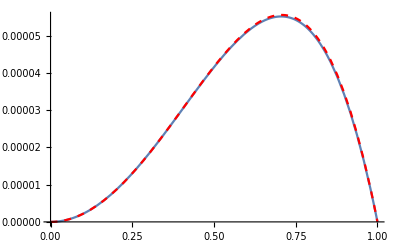

```mathematica
p1 = Plot[Re[N[(Λ/.growthrate)/. {Ca ->1.5, Bo-> 1.5, α -> 0.9, D->1}]], {κ, 0, 1}];
p2 = Plot[κ^2/3/1.5(D-κ^2)(1-α)^3/. {α -> 0.9, D->1}, {κ, 0, 1}, PlotStyle->{Red, Dashed}];
Show[p1,p2]
```

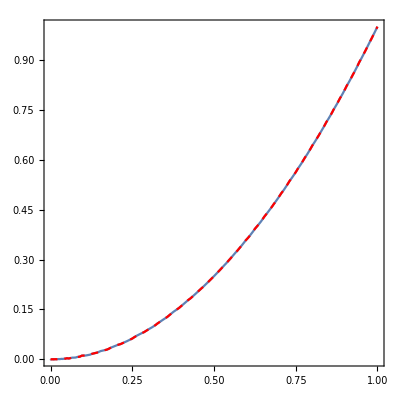

```mathematica
p1 =ContourPlot[Re[N[((Λ/.growthrate)/. {Ca ->0.1, Bo-> 0.1, α -> 0.5})]]==0, {κ, 0, 1}, {D, 1, 0}];
p2 = ContourPlot[k^2 (k^2-D)==0, {k, 0, 1}, {D, 1, 0},ContourStyle->{Dashed, Red}];
Show[p1,p2]
```

```mathematica
Series[N[(Λ/. growthrate)/.{Ca ->0.1, Bo-> 0.1}], {α,1, 0}]
```

{O[α-1]^1}

```mathematica
disprelguess= -SeriesCoefficient[detformula, {Λ, 0,0}]/SeriesCoefficient[detformula, {Λ, 0,1}]
```

(-BesselI[1,κ] (-((1/2 ⅈ α BesselI[2,α κ] BesselK[0,α κ]+1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ]))+(2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])) (-1/4 ⅈ α^2 BesselI[2,α κ] BesselK[1,α κ]-1/4 ⅈ α^2 BesselI[1,α κ] BesselK[2,α κ])+((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (-1/2 ⅈ α BesselK[1,α κ]^2+1/2 ⅈ α BesselK[0,α κ] BesselK[2,α κ])) (-1-1/2 κ^2 (-1+α^2-Log[α]))-BesselK[1,κ] ((-1/2 ⅈ α BesselI[1,α κ]^2+1/2 ⅈ α BesselI[0,α κ] BesselI[2,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ])+((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (-1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]-1/2 ⅈ α BesselI[0,α κ] BesselK[2,α κ])-(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (-1/4 ⅈ α^2 BesselI[2,α κ] BesselK[1,α κ]-1/4 ⅈ α^2 BesselI[1,α κ] BesselK[2,α κ])) (1+1/2 κ^2 (-1+α^2-Log[α]))-(-((ⅈ BesselI[1,α κ] BesselK[0,α κ]+ⅈ BesselI[0,α κ] BesselK[1,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ]))+(2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])) (-1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]-1/2 ⅈ α BesselI[0,α κ] BesselK[2,α κ])+(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (-1/2 ⅈ α BesselK[1,α κ]^2+1/2 ⅈ α BesselK[0,α κ] BesselK[2,α κ])) (1/2 BesselI[2,κ]+1/4 κ (κ BesselI[0,κ]-BesselI[1,κ]) (-1+α^2-Log[α]))-(((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (ⅈ BesselI[1,α κ] BesselK[0,α κ]+ⅈ BesselI[0,α κ] BesselK[1,α κ])-(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (1/2 ⅈ α BesselI[2,α κ] BesselK[0,α κ]+1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ])+(-1/2 ⅈ α BesselI[1,α κ]^2+1/2 ⅈ α BesselI[0,α κ] BesselI[2,α κ]) (2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ]))) (1/2 BesselK[2,κ]+1/4 κ (κ BesselK[0,κ]+BesselK[1,κ]) (-1+α^2-Log[α])))/(-ⅈ (κ BesselK[0,κ]+BesselK[1,κ]) (((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (ⅈ BesselI[1,α κ] BesselK[0,α κ]+ⅈ BesselI[0,α κ] BesselK[1,α κ])-(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (1/2 ⅈ α BesselI[2,α κ] BesselK[0,α κ]+1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ])+(-1/2 ⅈ α BesselI[1,α κ]^2+1/2 ⅈ α BesselI[0,α κ] BesselI[2,α κ]) (2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])))-2 ⅈ κ BesselK[1,κ] ((-1/2 ⅈ α BesselI[1,α κ]^2+1/2 ⅈ α BesselI[0,α κ] BesselI[2,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ])+((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (-1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]-1/2 ⅈ α BesselI[0,α κ] BesselK[2,α κ])-(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (-1/4 ⅈ α^2 BesselI[2,α κ] BesselK[1,α κ]-1/4 ⅈ α^2 BesselI[1,α κ] BesselK[2,α κ]))+2 ⅈ κ BesselI[1,κ] (-((1/2 ⅈ α BesselI[2,α κ] BesselK[0,α κ]+1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ]))+(2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])) (-1/4 ⅈ α^2 BesselI[2,α κ] BesselK[1,α κ]-1/4 ⅈ α^2 BesselI[1,α κ] BesselK[2,α κ])+((Bo+ⅈ κ (D-κ^2)) BesselI[0,κ]-ⅈ (D-ⅈ Ca κ-κ^2) BesselI[1,κ]+Ca BesselI[2,κ]) (-1/2 ⅈ α BesselK[1,α κ]^2+1/2 ⅈ α BesselK[0,α κ] BesselK[2,α κ]))-ⅈ (κ BesselI[0,κ]-BesselI[1,κ]) (-((ⅈ BesselI[1,α κ] BesselK[0,α κ]+ⅈ BesselI[0,α κ] BesselK[1,α κ]) (Bo BesselK[0,κ]+Ca κ BesselK[1,κ]+ⅈ (D-κ^2) (κ BesselK[0,κ]+BesselK[1,κ])+Ca BesselK[2,κ]))+(2 ⅈ κ (-D+κ^2) BesselK[1,κ]-Ca κ (BesselK[0,κ]+BesselK[2,κ])) (-1/2 ⅈ α BesselI[1,α κ] BesselK[1,α κ]-1/2 ⅈ α BesselI[0,α κ] BesselK[2,α κ])+(2 ⅈ κ (D-κ^2) BesselI[1,κ]-Ca κ (BesselI[0,κ]+BesselI[2,κ])) (-1/2 ⅈ α BesselK[1,α κ]^2+1/2 ⅈ α BesselK[0,α κ] BesselK[2,α κ])))

```mathematica
transformeddisprel = (disprelguess/ϵ)/.{Bo->ϵ, Ca->ϵ,κ->ϵ k };
```

```mathematica
Expand[N[(transformeddisprel+Conjugate[transformeddisprel])/. {ϵ -> 0.1, α ->1, k->1}]]
```

-((5.55112×10^-16+0. ⅈ)/((0.-0.0501876 ⅈ) ((0.-100.248 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))+(0.+193.556 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+10. ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D)))-(0.+10.0966 ⅈ) ((0.-0.000626042 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))+(0.+10. ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))-(0.+1.97077 ⅈ) ((0.+2.5 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+0.000626042 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))-(0.+100.248 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))+(0.+0.0100125 ⅈ) ((0.-2.5 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))+(0.+193.556 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))))-((1.42109×10^-13+0. ⅈ) D)/((0.-0.0501876 ⅈ) ((0.-100.248 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))+(0.+193.556 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+10. ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D)))-(0.+10.0966 ⅈ) ((0.-0.000626042 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))+(0.+10. ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))-(0.+1.97077 ⅈ) ((0.+2.5 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+0.000626042 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))-(0.+100.248 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))+(0.+0.0100125 ⅈ) ((0.-2.5 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))+(0.+193.556 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D))))+(10. Conjugate[-0.000625521 ((0.-100.248 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))+(0.+193.556 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+10. ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D)))-99.752 ((0.-0.000626042 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))+(0.+10. ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))-9.85384 ((0.+2.5 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+0.000626042 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))-(0.+100.248 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))+0.0500625 ((0.-2.5 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))+(0.+193.556 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))])/Conjugate[(0.-0.0501876 ⅈ) ((0.-100.248 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))+(0.+193.556 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+10. ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D)))-(0.+10.0966 ⅈ) ((0.-0.000626042 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))+(0.+10. ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))-(0.+1.97077 ⅈ) ((0.+2.5 ⅈ) (-0.0100375+(0.+0.0100125 ⅈ) (-0.01+D))-(0.+0.000626042 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))-(0.+100.248 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))+(0.+0.0100125 ⅈ) ((0.-2.5 ⅈ) (-2.01931+(0.+1.97077 ⅈ) (0.01-1. D))-(0.+0.248172 ⅈ) (20.2916+(0.+10.0966 ⅈ) (-0.01+D))+(0.+193.556 ⅈ) (0.000125104+1.0025 (0.1+(0.+0.1 ⅈ) (-0.01+D))-(0.+0.0500625 ⅈ) ((-0.01-0.01 ⅈ)+D)))]

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 1+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 1+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 1+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+ComplexInfinity+«3» encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

General::munfl: (1.4652×10^-259)/1496577676626844588240573268701473812127674924007424 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.95829×10^-263)/5986310706507378352962293074805895248510699696029696 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.55786×10^-267)/23945242826029513411849172299223580994042798784118784 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.